Mathematica Project : Kiva Crowdfunding Data Analysis

												-Graphics-

Kiva.orgis an online crowdfunding platform to extend financial services to poor and financially excluded people around the world.Kiva lenders have provided over $1.2 billion dollars in loans to over 2 million people.Kiva has provided a dataset of loans issued over the last two years.For the locations in which Kiva has active loans,our objective is to pair Kiva's data with additional data sources to estimate the welfare level of borrowers in specific regions,based on shared economic and demographic characteristics.

In this Mathematica project we are going to explore the different visualization techniques that can be used to find the some of the meaningful visual graphics from the given dataset. 
There are multiple dataset files provided by Kiva of which few of the data is unsupervised/unlabeled for which we are using machine learning methods to find the labels for unlabeled data.   
Comparison study  has been made on various methods of machine learning models such as Neural Networks, Support Vector Machines, Logistic Regression, Nearest Neighbour and Random Forest to identify best classifier methods and Neural Networks, Gaussian Process , Logistic Regression, Nearest Neighbour and Random Forest to identify best prediction methods for the given dataset. 
Since the dataset file are big and it takes more time to compute the output I have used only few of the rows of the dataset file. Data Preparation such as  replacing the missing values, removal of duplicate values, Data Integration and Data Transformation have been performed on the dataset.

## Data Exploration and Visualization:

Importing the dataset:

```mathematica
csv=Import["/Workspace/Kiva/DataSet1/Data Science for Good- Kiva Crowdfunding/kiva_loans.csv"];
header=csv[[1]];
data=csv[[2;;]];
dataset=Thread[header->#]&/@data//Map[Association]//Dataset;
```

Length of Dataset :

```mathematica
Length[dataset]
```

671205

Basic Visualizations of few of the Columns :

Below bar and pie chart describes the types of repayment intervals :

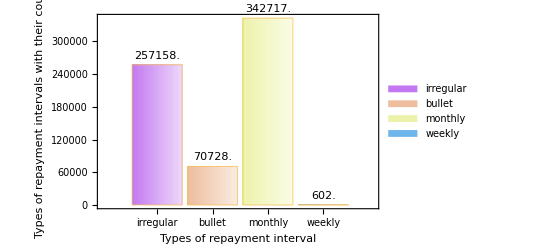

```mathematica
BarChart[Counts[dataset[All,"repayment_interval"]],ChartLabels->Automatic,ChartElementFunction->"FadingRectangle",ChartStyle->"Pastel", LabelingFunction->(Placed[Panel[NumberForm[N@#1]],Above]&), ChartLegends->Automatic,FrameLabel->{{"Types of repayment intervals with their count",None},{"Types of repayment interval",None}},Frame->{{True,None},{True,None}}]
```

```mathematica
PieChart[Counts[dataset[All,"repayment_interval"]],ChartLabels-> Automatic,ChartElementFunction->"GlassSector",ChartStyle->"Pastel",ChartLegends->Automatic]
```

-Graphics-

Most/Top 10 frequent countries who got loans :

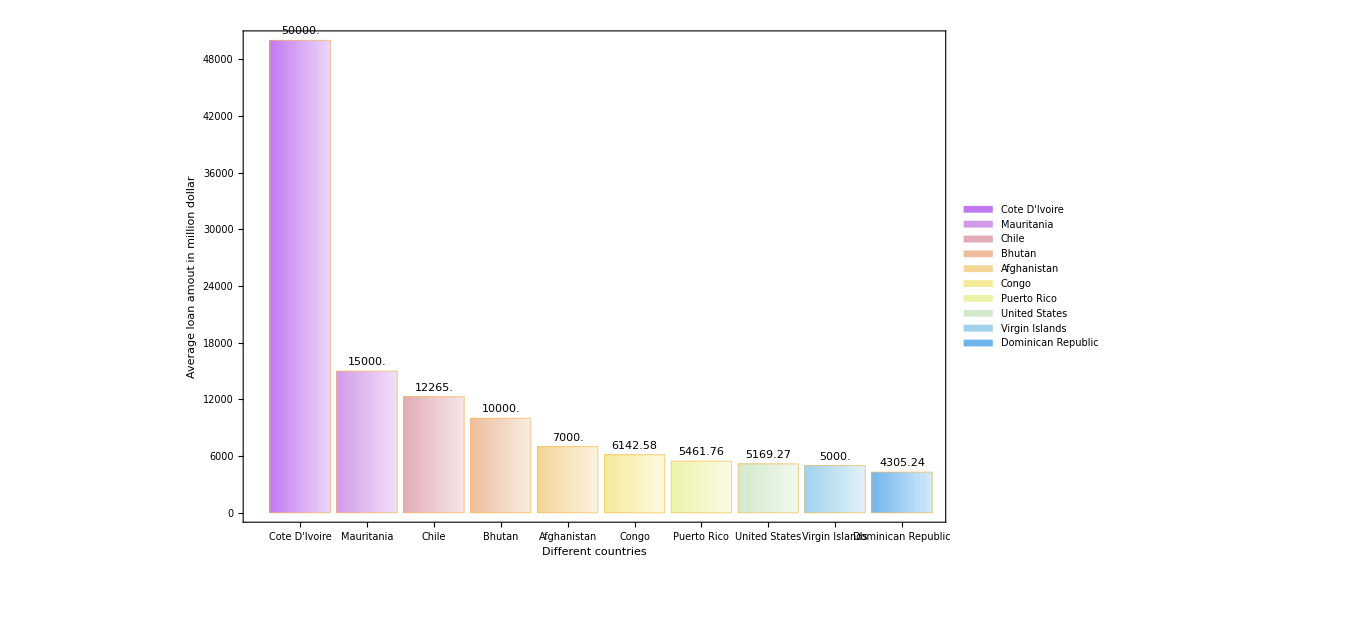

```mathematica
BarChart[Sort[dataset[GroupBy["country"],Mean,"loan_amount"],Greater][[1;;10]],ChartElementFunction->"FadingRectangle",ChartStyle->"Pastel", LabelingFunction->(Placed[Panel[NumberForm[N@#1]],Above]&), ChartLegends->Automatic,ImageSize->{1000,700},FrameLabel->{{"Average loan amout in million dollar",None},{"Different countries",None}},ChartLabels-> Automatic,Frame->{{True,None},{True,None}}]
```

Mean loan amount by different sectors:

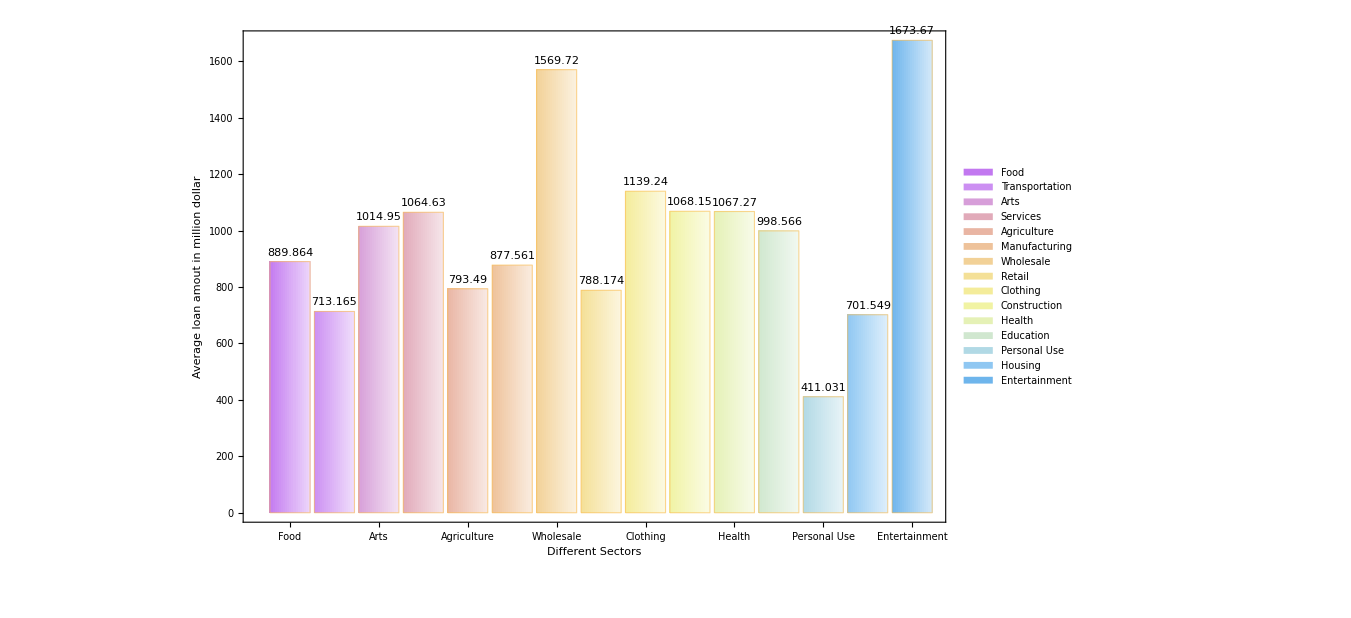

```mathematica
BarChart[trainset[GroupBy["sector"],Mean,"loan_amount"],ChartElementFunction->"FadingRectangle",ChartStyle->"Pastel", LabelingFunction->(Placed[Panel[NumberForm[N@#1]],Above]&), ChartLegends->Automatic,ImageSize->{1000,700},FrameLabel->{{"Average loan amout in million dollar",None},{"Different Sectors",None}},ChartLabels-> Automatic,Frame->{{True,None},{True,None}}]
```

Mean loan amount by Top 10 different activities:

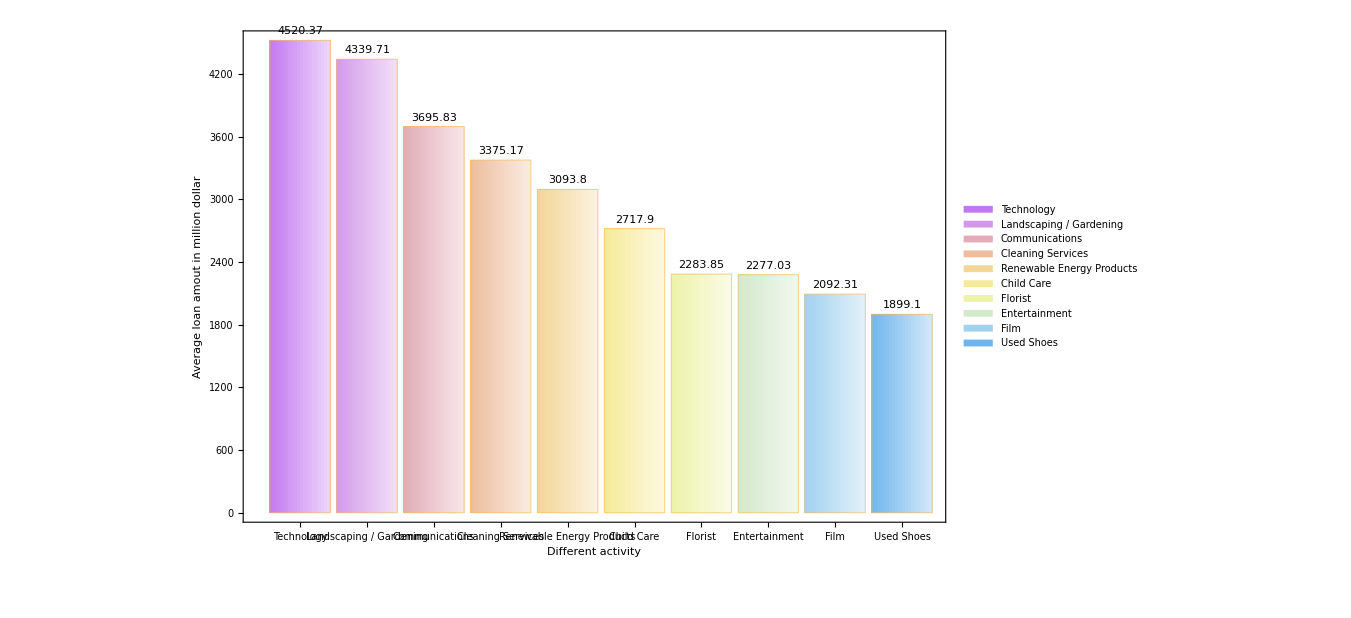

```mathematica
BarChart[Sort[trainset[GroupBy["activity"],Mean,"loan_amount"],Greater][[1;;10]],ChartElementFunction->"FadingRectangle",ChartStyle->"Pastel", LabelingFunction->(Placed[Panel[NumberForm[N@#1]],Above]&), ChartLegends->Automatic,ImageSize->{1000,700},FrameLabel->{{"Average loan amout in million dollar",None},{"Different activity",None}},ChartLabels-> Automatic,Frame->{{True,None},{True,None}}]
```

Mean loan amount by top 10 different regions(locations within countries) :

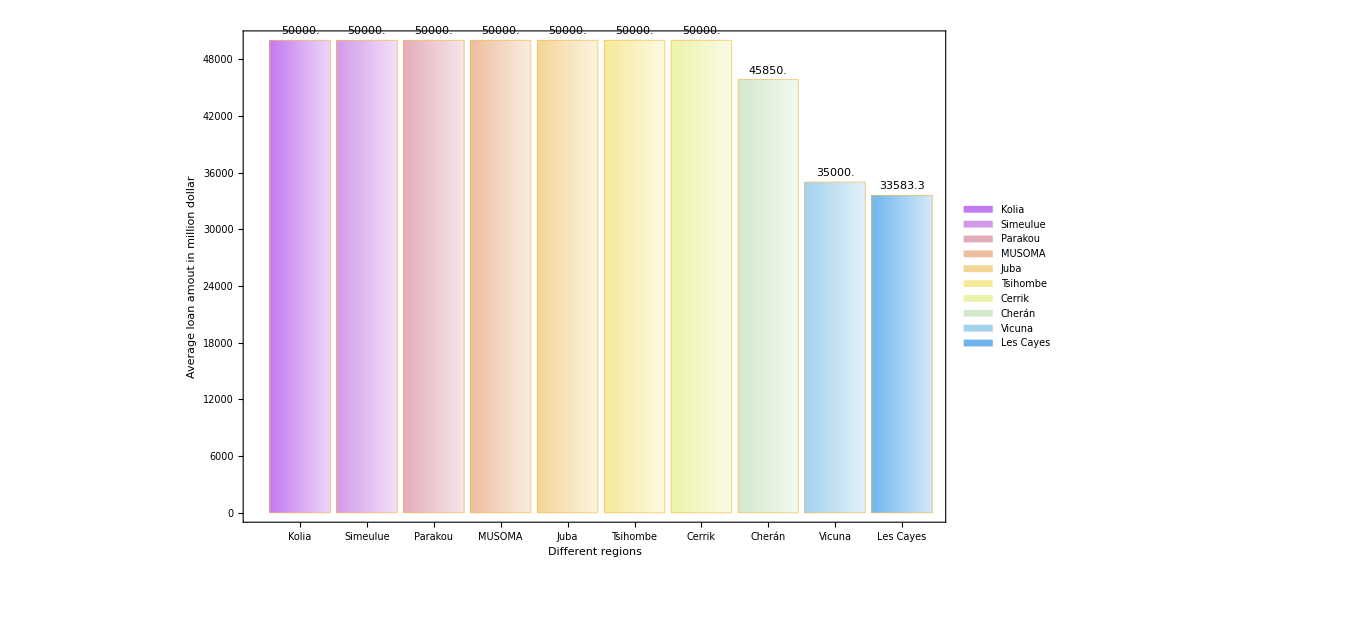

```mathematica
BarChart[Sort[trainset[GroupBy["region"],Mean,"loan_amount"],Greater][[1;;10]],ChartElementFunction->"FadingRectangle",ChartStyle->"Pastel", LabelingFunction->(Placed[Panel[NumberForm[N@#1]],Above]&), ChartLegends->Automatic,ImageSize->{1000,700},FrameLabel->{{"Average loan amout in million dollar",None},{"Different regions",None}},ChartLabels-> Automatic,Frame->{{True,None},{True,None}}]
```

Below pie chart shows “Loan theme specifically for Kiva V.S. Loan theme not specifically for Kiva” : 

For this we need to load other dataset given by Kiva:

```mathematica
csv=Import["/Workspace/Kiva/DataSet1/Data Science for Good- Kiva Crowdfunding/loan_themes_by_region.csv"];
header=csv[[1]];
data=csv[[2;;]];
datasetforkiva=Thread[header->#]&/@data//Map[Association]//Dataset;
```

```mathematica
PieChart[Counts[datasetforkiva[All,"forkiva"]],ChartLabels-> Automatic,ChartElementFunction->"GlassSector",ChartStyle->"Pastel",ChartLegends->Automatic]
```

-Graphics-

Below WordCloud generates a word cloud graphic in which the reasons for loan are sized according to their multiplicity in the list.

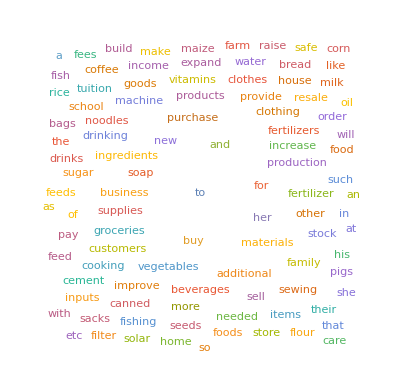

```mathematica
WordCloud[WordCounts[ToString[dataset[All,"use"]]]]
```

Below WordCloud generates a word cloud graphic in which the countries are sized according to their multiplicity in the list.

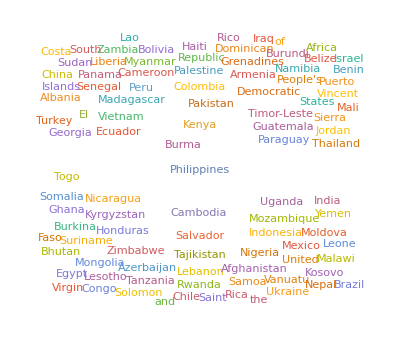

```mathematica
WordCloud[WordCounts[ToString[dataset[All,"country"]]]]
```

## Depth Analysis on one of the column in the dataset:

Below we analyse on “Borrower Gender’s” column to find who takes more loan and to find is it group of people or single person taking more loan?

Some of the entries are:
female - i.e. individual gender
female, female, ... - i.e. group of all females
male, male, ... - i.e. group of all males
female, male, female, ... - i.e. group of females and males

Since the dataset is huge and Mathematica takes more time to load we are just taking the first 50000 observations for analysis.

```mathematica
gender =dataset[[1;;50000]];
```

We are replacing the missing values with some string such as “unknown” so that we can even display the missing values in the dataset in the plot.

```mathematica
datasetgender =gender[All]/.""->"unknown";
```

Count the number of borrowers: 
1. WordCount is used to find the number words in each observations/rows in the column borrower_genders
2. Using Total function to perform the total of the entire continues values

```mathematica
listWords = Normal[WordCount[Normal[datasetgender[All,"borrower_genders"]]]];
```

Example :

```mathematica
listWords[[1;;50]]
```

{1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
wordCount = Total[listWords]
```

94339

From the above output we come to know that for 50000 observations we have 94,339 people taking the loans.

Now let’s identify from the list which all the observations have group loan.
Here we are replacing all those values less than or equal to 1 to “0”(because in these observations the loan was taken by single person ) and all those observations greater than 1 are replaced with 1 (becasue in these observations the loan was taken by group of people)

```mathematica
listWordGroup=listWords/.x_/;x≤1->0/.x_/;x>1->1;
```

Example :

```mathematica
listWordGroup[[1;;50]]
```

{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

In the above output we can see there are 1’s which means in those observations the loan was taken/provided to group of people with/without same gender.

Now let’s find out the number of female borrowers

```mathematica
listFemale = StringCount[Normal[datasetgender[All,"borrower_genders"]],"female"];
```

Example :

```mathematica
listFemale[[1;;50]]
```

{1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,8,1,1,1,1,1,1,1,1,1,1,1,1,1,0}

Form the above output we can see that some of the observations have values such as 2,8,... which means these are the observations where a loan was provided to group of people and of these 2,8... are the number females in that group and “1” means the loan was provide to single female and “0” means loan was provide to male in the respective observation.

Finding the total female borrower count :

```mathematica
borrowerFemale = Total[listFemale]
```

77310

Finding the total unknown borrower count :

```mathematica
listUnknow = StringCount[Normal[datasetgender[All,"borrower_genders"]],"unknow"];
```

Example  :

```mathematica
listUnknow[[1050;;1100]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

From the above output we can see that there is one (“1”) in the observations which means that observation in  dataset has missing borrower gender value.

Total Number of missing values  in borrower gender column:

```mathematica
borrowerUnknow = Total[listUnknow]
```

631

Finding number of males:

```mathematica
listMale  =listWords - listFemale-listUnknow;
```

Total Number of males :

```mathematica
borrowerMale = Total[listMale]
```

16398

We haven’t used the above command(StringCount[Normal[datasetgender[All,”borrower_genders”]],”female”]) to find the male count because the regex of StringCount match male with female becasue female has substring male in it.

Example :

```mathematica
Total[StringCount[Normal[datasetgender[All,"borrower_genders"]],"male"]]
```

93708

From the above we can see that total male count is almost close to total word count and summing male,female,unknown counts will be more than total count. Hence we followed different process to calculate the total male count as show above(listMale  =listWords - listFemale-listUnknow)

Lets append the above obtained list of male,female and unknown, group data to original dataset.

```mathematica
datasetgender = datasetgender//Transpose//Append["borrower_total_count"->listWords]//Transpose;
datasetgender = datasetgender//Transpose//Append["borrower_female_count"->listFemale]//Transpose;
datasetgender = datasetgender//Transpose//Append["borrower_unknown_count"->listUnknow]//Transpose;
datasetgender = datasetgender//Transpose//Append["borrower_male_count"->listMale]//Transpose;
datasetgender = datasetgender//Transpose//Append["borrower_group"->listWordGroup]//Transpose;
```

So final dataset looks like :

```mathematica
datasetgender[[1;;10]]
```

Dataset[<>]

Below we are performing various operations to convert the binary data we obtained above to categorical data so that visualization would be easy:

```mathematica
datasetgender =datasetgender[All,Append[#,"borrower_gender_class"->If[FullSimplify[#"borrower_male_count" == 0&&#"borrower_group"==1],"all females",If[FullSimplify[#"borrower_female_count" == 0&&#"borrower_group"==1],"all males",If[FullSimplify[#"borrower_male_count" > 0&&#"borrower_female_count">0&&#"borrower_group"==1],"males and females",If[FullSimplify[#"borrower_male_count" == 1],"male",If[FullSimplify[#"borrower_female_count" == 1],"female","Unknown"]]]]]]&];
```

Example :

```mathematica
datasetgender[[1;;10]]
```

Dataset[<>]

The last column of the above dataset output we can see we have required categorical data to represent in the plot

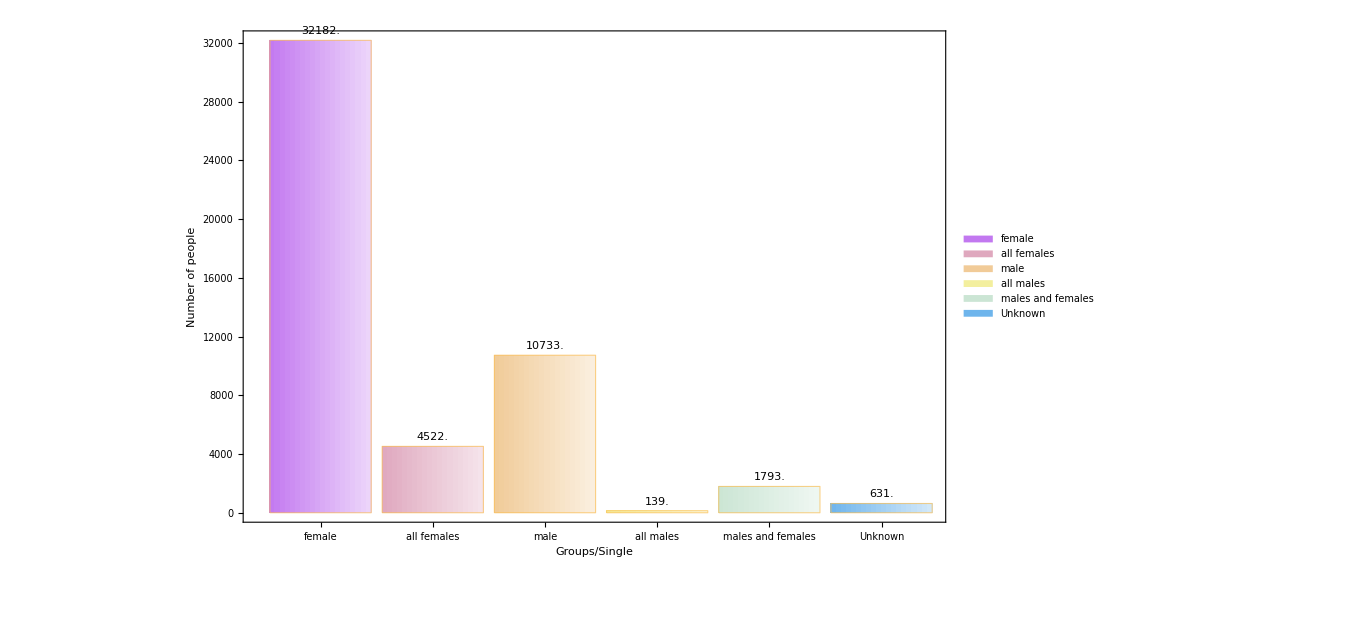

```mathematica
BarChart[Counts[test[All,"borrower_gender_class"]],ChartElementFunction->"FadingRectangle",ChartStyle->"Pastel", LabelingFunction->(Placed[Panel[NumberForm[N@#1]],Above]&), ChartLegends->Automatic,ImageSize->{1000,700},FrameLabel->{{"Number of people",None},{"Groups/Single",None}},ChartLabels-> Automatic,Frame->{{True,None},{True,None}}]
```

Finally we have the plot which clearly shows us the count for each category
Here :
“female” means only single female borrower in the respective observation. 
 “all female” means loan was provided to a group, of which the gender of all the people was female.
 “male”means only single male borrower in the respective observation. 
“all male” means loan was provided to a group, of which the gender of all the people was male.
“males and females” means that loan was provided to a group, of which the group had both gender people. 
“Unknown” represents the count of missing values.

## Time series analysis on funded amount and disbursed time

Here we will perform graphical analysis on how amount was funded with respect to time.
To perform TimeSeries we have do some data transformation as our given dataset is not the input format for TimeSeries format .

Firstly we are taking just 1000 rows to perform the action as computations on the entire dataset is taking more time.
As are just focusing on date and since our time in disbursed column is of the format (2014-01-01 12:23:00+00:00 ) we performing splitting the data item value so that we just get First part of it (i.e, 2014-01-01)

```mathematica
f = StringSplit[Normal[dataset[All,"disbursed_time"]][[1;;1000]]," "];
```

Now we are creating an empty list to append the required time values into a list.

```mathematica
p = {};
For [i =1,i≤ Length[f],i++,AppendTo[p,f[[i]][[1]]]]
```

Now are replacing the character “-” to “/” as the time input should be of the (2014/01/01)

```mathematica
datap = {};
datap= StringReplace[p,"-"-> "/"];
```

Now we are taking the respective funded amount values and adding both time and funded amount to  list of required format.

```mathematica
c = Normal[dataset[All,"funded_amount"]][[1;;1000]];
```

Here we are adding both of them to  a list list.

```mathematica
finaldata = {};
For [i =1,i≤ Length[f],i++,AppendTo[finaldata,{datap[[i]],c[[i]]}]]
```

Below we are passing the modified/final data to TimesSeries.
The time series represents  a time series specified by time-value pairs, in the following the disbursed time and the target variable, the funded amount.

```mathematica
t = TimeSeries[finaldata,DateFunction:>(DateList[{#,{"Year","Month","Day"}}]&)]
```

TimeSeries[…]

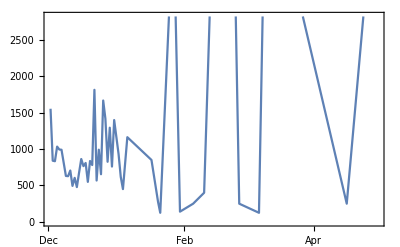

```mathematica
DateListPlot[t]
```

Above graph consists of only the time data between months Dec 2013 to April 2014
From the above graph we can observe that till mid of Jan 2014 the max amount funded was 1500(million dollar) but after mid of Jan 2014 we can see that funded amount grew drastically.

## World map view of each country obtaining loan

Here we will display a pointer for each country who are obtaining loans on world map 

Latitude and Longitude of each countries are stored in a different dataset, so we need to load the dataset:

```mathematica
csv=Import["/Workspace/Kiva/DataSet1/World Countries and Continents Details/Countries Longitude and Latitude.csv"];
header1=csv[[1]];
data1=csv[[2;;]];
latlon=Thread[header1->#]&/@data1//Map[Association]//Dataset;
```

“latlonpair” function is used in order to pair up to columns(latitude and longitude) of the dataset

```mathematica
latlonpair[xValues_,yValues_]:=({xValues[[#]],yValues[[#]]})&/@Range[Min[Length[xValues],Length[yValues]]];
```

Below we are sending the latitude and longitude values to “loatlonpair” function to pair up and perform a list plot of the obtained pair list.

{-86.2419,15.2}

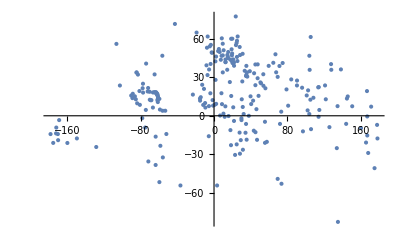

```mathematica
latlongPair1=latlonpair[latlon[All,"latitude"], latlon[All,"longitude"]];
latlongPair1[[100]]
ListPlot[latlongPair1]
```

From the obtained latitude and longitude pair we are plotting them on Word Map using GeoGraphics function:

```mathematica
GeoGraphics[{Red,PointSize[.01],Point@GeoPosition@latlongPair1[[5;;]]},GeoRange->"World",GeoProjection->"Mollweide",GeoGridLines->Quantity[5,"AngularDegrees"],GeoBackground->"ContourMap", ImageSize->Full] //Quiet
```

-Graphics-

## Machine learning Model Building:

#### Exploring various Classification methods and options available:

#### Preparing Dataset :

Below we are importing the dataset for classification. Kiva have provided a labeled dataset set in which one of the column has cluster’s(column name DHSCLUST) by default  based on the latitude and longitude of the loan borrowers.
And we are removing the duplicate values from the dataset.

```mathematica
csv=Import["/Workspace/Kiva/DataSet1/Kiva/KIVA.DHSv4.csv"];
header=csv[[1]];
data=csv[[2;;]];
trainset=Thread[header->#]&/@data//Map[Association]//Dataset;
data = trainset;
data1 = DeleteDuplicates[data[All,{"DHSCLUST","DHS.lat","DHS.lon","country","region","MPI.median","Nb.HH","AssetInd.median","URBAN_RURA","Nb.Electricity","Nb.fuel","Nb.floor","Nb.imp.sanitation","Nb.imp.water","Median.educ","Nb.television","Nb.phone","names"}]];
```

```mathematica
data1[[1;;10]]
```

Dataset[<>]

Below we are converting the give data values to some meaningful values:

```mathematica
data1 = data1[All,Append[#,"Nb.Electricity"-> N[100*(#"Nb.Electricity")/#"Nb.HH",3]]&];
data1 = data1[All,Append[#,"Nb.fuel"-> N[100*(#"Nb.fuel")/#"Nb.HH",3]]&];
data1 = data1[All,Append[#,"Nb.floor"-> N[100*(#"Nb.floor")/#"Nb.HH",3]]&];
data1 = data1[All,Append[#,"Nb.imp.sanitation"-> N[100*(#"Nb.imp.sanitation")/#"Nb.HH",3]]&];
data1 = data1[All,Append[#,"Nb.imp.water"-> N[100*(#"Nb.imp.water")/#"Nb.HH",3]]&];
data1 = data1[All,Append[#,"Nb.television"-> N[100*(#"Nb.television")/#"Nb.HH",3]]&];
data1 = data1[All,Append[#,"Nb.phone"-> N[100*(#"Nb.phone")/#"Nb.HH",3]]&];
```

Since the “AssetInd.median” values cannot be negative we need to convert them to postive value which we are doing below;

```mathematica
data1= data1[All,Append[#,"URBAN_RURA"->If[ToString[#"URBAN_RURA"]== "U",1,0]]&];
min = Min[Normal[data1[All,"AssetInd.median"]]][[1]];
max = Max[Normal[data1[All,"AssetInd.median"]]][[1]];
```

```mathematica
data2 =data1[All,Append[#,"AssetInd.median"-> N[(100/(max-(min)))*(#"AssetInd.median"-min),3]]&];
```

Now the dataset has meaningful values required for analysis.

```mathematica
cluster = data2[All,<|  "DHSCLUST"->"DHSCLUST","DHS.lat"-> "DHS.lat","DHS.lon"-> "DHS.lon","region" -> "region","MPI_cluster"-> "MPI.median" ,"wealth_index"-> "AssetInd.median" , "urbanity"-> "URBAN_RURA" ,  "ratio_electricity"-> "Nb.Electricity",
                        "ratio_sanitation"-> "Nb.imp.sanitation","ratio_water"-> "Nb.imp.water" ,  "ratio_phone"-> "Nb.phone",
                         "ratio_nakedSoil"-> "Nb.floor", "ratio_cookingFuel"-> "Nb.fuel",  "location_details"-> "names","television"-> "Nb.television","country"-> "country"|>];
```

```mathematica
cluster[[1;;5]]
```

Dataset[<>]

Since latitude and longitude are in degrees we need to convert them to radians because input to classify should always be meaningful numerical values than in degrees hence  we are transforming the data  :

```mathematica
datad= cluster;
datad =datad[All,Append[#,"latradian"-> N[(#"DHS.lat")*0.01745329,5]]&];
datad =datad[All,Append[#,"lonradian"-> N[(#"DHS.lon")*0.01745329,5]]&];
datad =datad[All,Append[#,"latlonradian"-> {#"latradian",#lonradian}]&];
```

```mathematica
datad[[1;;5]]
```

Dataset[<>]

The last column in the above output shows that latitude and longitude are paired and converting to radians.

Finally, dataset is ready to apply for different classify model !!!!!

Dividing the dataset in to train and test list:

```mathematica
train ={};
test = {};
For[i=1,i≤Length[datad],i++,If[RandomInteger[{1,Length[datad]}]<Length[datad] 70/100,AppendTo[train,Normal[datad[i,All]]],AppendTo[test,Normal[datad[i,All]]]]]
train = Dataset[train];
test =Dataset[test];
```

Creating an Association for each latitude and logitude with respective cluster given in the dataset for train and test set.

```mathematica
trainlist = {};
testlist={};
For[i=1,i≤ Length[train],i++,list = AppendTo[trainlist,Normal[train[i,"latlonradian"]]-> Normal[train[i,"DHSCLUST"]]]]
For[i=1,i≤ Length[test],i++,list2 = AppendTo[testlist,Normal[test[i,"latlonradian"]]-> Normal[test[i,"DHSCLUST"]]]]
```

Train a classifier function on labeled examples:

#### Logistic Regression :

```mathematica
classLR=Classify[trainlist, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[classLR]
```

Classifier information
Input type | {Nominal,Nominal}
Number of classes | 460
Method | LogisticRegression
Accuracy | 73.4 % ± 2.9 %
Loss | 1.95 ± 0.17
Single evaluation time | 17.8 ms/example
Batch evaluation speed | 3.46 examples/ms
Classifier memory | 602. kB
Training examples used | 2424 examples
Training time | 11.1 s
 |

Now the model is ready with 73.4%(approximate) accuracy as show above output and lets apply the test set to find how accurate model was able to classify the testset

```mathematica
cmLR=ClassifierMeasurements[classLR,testlist];
```

```mathematica
cmLR/@{"Accuracy","Error"}//TableForm
```

0.688933
0.311067

We see that using “Logistic Regression” model we can classify the testset with an accuracy of 68.8%.

Now let’s see the relationship between Accuracy and Rejection using “Logistic Regression” model.

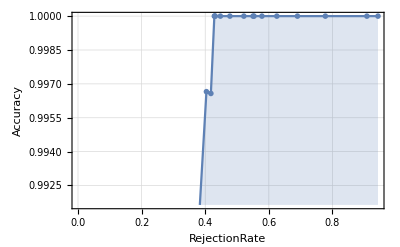

```mathematica
cmLR["AccuracyRejectionPlot"]
```

From the above output we can see that model can classify accurately (100%) when the rejection rate is above 50%.

#### NearestNeighbors:

Now lets classify train dataset with another classify model “NearestNeighbors”

```mathematica
classNN=Classify[trainlist, Method->{"NearestNeighbors","NeighborsNumber"->1}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[classNN]
```

Classifier information
Input type | {Nominal,Nominal}
Number of classes | 460
Method | NearestNeighbors
Accuracy | 85. % ± 1.2 %
Loss | 1.57 ± 0.096
Single evaluation time | 16.1 ms/example
Batch evaluation speed | 3.23 examples/ms
Classifier memory | 874. kB
Training examples used | 2424 examples
Training time | 2.07 s
 |

Now the model is ready with 85%(approximate) accuracy as show above output and lets apply the test set to find how accurate model was able to classify the testset

```mathematica
cmNN=ClassifierMeasurements[classNN,testlist];
cmNN/@{"Accuracy","Error"}//TableForm
```

0.851446
0.148554

We see that using “NearestNeighbors” model we can classify the testset with an accuracy of 85.1%.
Now let’s see the relationship between Accuracy and Rejection using “NearestNeighbors” model.

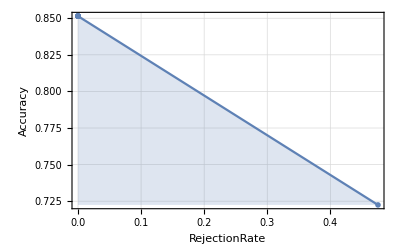

```mathematica
cmNN["AccuracyRejectionPlot"]
```

From the above output we can see that model can classify accurately (100%) when the rejection rate is low 0%.

From this we come to know that “NearestNeighbors” is able to classify our dataset better than “Logistic Regression”

#### RandomForest:

Now lets classify train dataset with another classify model “RandomForest”

```mathematica
classRF=Classify[trainlist, Method->"RandomForest"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[classRF]
```

Classifier information
Input type | {Nominal,Nominal}
Number of classes | 460
Method | RandomForest
Accuracy | 81.2 % ± 2.5 %
Loss | 4.59 ± 0.052
Single evaluation time | 18.9 ms/example
Batch evaluation speed | 1.98 examples/ms
Classifier memory | 2.27 MB
Training examples used | 2424 examples
Training time | 3.55 s
 |

Now the model is ready with 81.2%(approximate) accuracy as show above output and lets apply the test set to find how accurate model was able to classify the testset

```mathematica
cmRF=ClassifierMeasurements[classRF,testlist];
cmRF/@{"Accuracy","Error"}//TableForm
```

0.799601
0.200399

We see that using “RandomForest” model we can classify the testset with an accuracy of 79.9%.
From this we come to know that “RandomForest” is able to classify our dataset better than “Logistic Regression” but not as better as “NearestNeighbors”

#### NeuralNetwork:

Now lets classify train dataset with another classify model “NeuralNetwork”

```mathematica
classNNW=Classify[trainlist, Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[classNNW]
```

Classifier information
Input type | {Nominal,Nominal}
Number of classes | 460
Method | NeuralNetwork
Accuracy | 43. % ± 3.2 %
Loss | 4.91 ± 0.073
Single evaluation time | 23.2 ms/example
Batch evaluation speed | 1.81 examples/ms
Classifier memory | 1.73 MB
Training examples used | 2424 examples
Training time | 20.9 s
 |

Now the model is ready with 43%(approximate) accuracy as show above output and lets apply the test set to find how accurate model was able to classify the testset

```mathematica
cmNNW=ClassifierMeasurements[classNNW,testlist];
cmNNW/@{"Accuracy","Error"}//TableForm
```

0.400798
0.599202

We see that using “NeuralNetwork” model we can classify the testset with an accuracy of 40%.

Now let’s see the relationship between Accuracy and Rejection using “NeuralNetwork” model.

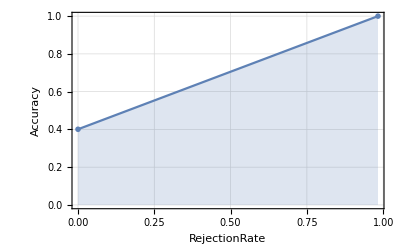

```mathematica
cmNNW["AccuracyRejectionPlot"]
```

From this we come to know that “NeuralNetwork” is not better classifier to be used for this dataset above classifier(Logistic Regression, Random Forest and NearestNeighbors) are better than “NeuralNetwork”

#### Let’s Examine how Accuracy and Error rate varies after apply constrains such as Performance Goal(TrainingSpeed and Memory) and Time Goal:

Here we are understanding how the accuracy and error rate varies on applying constrains such as TrainingSpeed and memory(classifier uses less memory to perform actions) and Time Goal(makes the classifier to perform the classification within the specified time interval)
Here we are excluding SVM because its taking huge time to compute than other.

Let’s start with default option without introducing any constrains and print the Accuracy and Error rate respectively :
Here in the output first value is the Accuracy and Second Value is Error rate with respective classfier models.

```mathematica
AssociationMap[ ClassifierMeasurements[
Classify[trainlist,Method->#],testlist, {"Accuracy","Error"}]&,{"RandomForest", "NaiveBayes","NearestNeighbors","LogisticRegression","NeuralNetwork"}]
```

<|RandomForest→{0.799601,0.200399},NaiveBayes→{0.851446,0.148554},NearestNeighbors→{0.760718,0.239282},LogisticRegression→{0.824526,0.175474},NeuralNetwork→{0.443669,0.556331}|>

Now let’s introduce the first constrain “TrainingSpeed” and examine the output:

```mathematica
AssociationMap[ ClassifierMeasurements[
Classify[trainlist,Method->#,PerformanceGoal->"TrainingSpeed"],testlist, {"Accuracy","Error"}]&,{"RandomForest", "NaiveBayes","NearestNeighbors","LogisticRegression","NeuralNetwork"}]
```

<|RandomForest→{0.767697,0.232303},NaiveBayes→{0.851446,0.148554},NearestNeighbors→{0.760718,0.239282},LogisticRegression→{0.56331,0.43669},NeuralNetwork→{0.372881,0.627119}|>

From the above output we can see that becasue of introducing the constrain “TrainingSpeed” the accuracy is reduced for most of the models except  NaiveBayes and NearestNeighnors.

Now let’s introduce another Constrain Memory:

```mathematica
AssociationMap[ ClassifierMeasurements[
Classify[trainlist,Method->#,PerformanceGoal->{"TrainingSpeed", "Memory"}],testlist, {"Accuracy","Error"}]&,{"RandomForest", "NaiveBayes","NearestNeighbors","LogisticRegression","NeuralNetwork"}]
```

<|RandomForest→{0.696909,0.303091},NaiveBayes→{0.851446,0.148554},NearestNeighbors→{0.791625,0.208375},LogisticRegression→{0.56331,0.43669},NeuralNetwork→{0.352941,0.647059}|>

Now we see that again the accuracy rate is reduced and another observation is that this time even for “NearestNeighbors” the accuracy was reduced.

Now let’s set the training time to a specified number than default and examine the output. Here model training will happen within 5secs even though model may need more time to train itself.

```mathematica
AssociationMap[ ClassifierMeasurements[
Classify[trainlist,Method->#,TimeGoal->5],testlist, {"Accuracy","Error"}]&,{"RandomForest", "NaiveBayes","NearestNeighbors","LogisticRegression","NeuralNetwork"}]
```

<|RandomForest→{0.812562,0.187438},NaiveBayes→{0.851446,0.148554},NearestNeighbors→{0.791625,0.208375},LogisticRegression→{0.830508,0.169492},NeuralNetwork→{0.0568295,0.94317}|>

Form the above output we can say that most of the model’s accuracy rate increased becasue by default they might be taking less than 5secs to compute. However, Accuracy rate for NeuralNetwork reduced drastically from 37.2% to 5% becasue NeuralNetwork need more time to train.

Now let’s reduced the train time to just 0.1sec and examine the output :

```mathematica
AssociationMap[ ClassifierMeasurements[
Classify[trainlist,Method->#,TimeGoal->0.1],testlist, {"Accuracy","Error"}]&,{"RandomForest", "NaiveBayes","NearestNeighbors","LogisticRegression","NeuralNetwork"}]
```

<|RandomForest→{0.799601,0.200399},NaiveBayes→{0.829511,0.170489},NearestNeighbors→{0.760718,0.239282},LogisticRegression→{0.658026,0.341974},NeuralNetwork→{0.0538385,0.946162}|>

From the above output we see that RandomForest and NearestNeighbors the accuracy remained same and for all other models accuracy reduced especially for NeuralNetwork (drastic change) in accuracy when compared to default training time

## Prediction:

For prediction we are using the unlabeled data from a different dataset where DHSCLUST is not know and we try predict the DHSCLUST from the given latitude and logitude. 

Here we will load 3 different dataset are used because latitude and longitude are stored in one dataset for a particular country (loan_coords.csv) and load information and other dataset variables are stored in different dataset(loans.csv) and country names are stored in other dataset(kiva_country _profile _variables.csv).

We are merging the first 2 dataset from unique identifier loan_id and then merging with other dataset with country name. 

After all these dataset transformation and creation we have final dataset that we need to predict the DHSCLUST for all of the entries.

```mathematica
csv=Import["/Workspace/Kiva/Additionalkivasnapshot/loan_coords.csv"];
header=csv[[1]];
data=csv[[2;;]];
loancoords=Thread[header->#]&/@data//Map[Association]//Dataset;
```

```mathematica
csv=Import["/Workspace/Kiva/loans.csv"];
header=csv[[1]];
data=csv[[2;;]];
loansextended=Thread[header->#]&/@data//Map[Association]//Dataset;
```

```mathematica
csv=Import["/Workspace/Kiva/Dataset1/kiva_country_profile_variables.csv"];
header=csv[[1]];
data=csv[[2;;]];
undata=Thread[header->#]&/@data//Map[Association]//Dataset;
```

```mathematica
dataset1 =JoinAcross[Normal[loansextended],Normal[loancoords],Key["loan_id"]];
```

```mathematica
loanswithcoords = JoinAcross[dataset,Normal[undata],Key["country_name"]];
```

```mathematica
x =Dataset[loanswithcoords];
```

Here we are taking the values of only below defined countries as these are the countries which are occurring mostly.

```mathematica
loans =x[Select[#"country_name"=="Philippines"||#"country_name"=="Colombia"||#"country_name"=="Armenia"||#"country_name"=="Kenya"||#"country_name"=="Haiti"&]];
```

Here we are performing conversion of latitude and longitude in degree to radians.

```mathematica
datad1= loans;
datad1 =datad1[All,Append[#,"latradian"-> N[(#"latitude")*0.01745329,5]]&];
datad1 =datad1[All,Append[#,"lonradian"-> N[(#"longitude")*0.01745329,5]]&];
datad1 =datad1[All,Append[#,"latlon"-> {#"latradian",#"lonradian"}]&];
datad1[[1;;10]]
```

Dataset[<>]

Above is the final dataset after merging all variables from different dataset’s.

While working on classification we had divided the labeled data for test and train but now we are using the complete dataset without dividing as we have test data from different dataset.

Below we are creating trainset

```mathematica
trainlistpredict = {};
For[i=1,i≤ Length[datad],i++,list = AppendTo[trainlistpredict,Normal[datad[i,"latlonradian"]]-> Normal[datad[i,"DHSCLUST"]]]]
```

Here we are creating the testset from the unlabeled data which we obtained above from 3 different datasets

```mathematica
testlistpredict = {};
For[i=1,i≤ Length[datad1],i++,list = AppendTo[testlistpredict,Normal[datad1[i,"latlon"]]]]
```

#### LinearRegression:

Let’s perform prediction using LinearRegression model from the train set.

```mathematica
lr =Predict[trainlistpredict,Method->"LinearRegression"]
```

PredictorFunction[…]

Below we are performing the prediction on unlabeled dataset(test set) from above obtained modeled.

```mathematica
predicttestlist = {};
$RecursionLimit=Length[testlistpredict];
For[i=1,i≤ Length[testlistpredict],i++,predicttestlist = AppendTo[predicttestlist,lr[testlistpredict[[i]]]]];
predicttestlist[[1]]
```

455.768

The above output is the predicted value(DHSCLUST) for one of the latitude and longitude given.

#### NearestNeighbors:

Let’s perform prediction using NearestNeighbors model from the train set.

```mathematica
nn=Predict[trainlistpredict,Method->"NearestNeighbors"]
```

PredictorFunction[…]

Below we are performing the prediction on unlabeled dataset(test set) from above obtained modeled.

```mathematica
predicttestlist = {};
$RecursionLimit=Length[testlistpredict];
For[i=1,i≤ Length[testlistpredict],i++,predicttestlist = AppendTo[predicttestlist,nn[testlistpredict[[i]]]]];
predicttestlist[[1]]
```

256.

The above output is the predicted value(DHSCLUST) for one of the latitude and longitude given.

#### RandomForest:

Let’s perform prediction using RandomForest model from the train set.

```mathematica
rf=Predict[trainlistpredict,Method->"RandomForest"]
```

PredictorFunction[…]

Below we are performing the prediction on unlabeled dataset(test set) from above obtained modeled.

```mathematica
predicttestlist = {};
$RecursionLimit=Length[testlistpredict];
For[i=1,i≤ Length[testlistpredict],i++,predicttestlist = AppendTo[predicttestlist,rf[testlistpredict[[i]]]]];
predicttestlist[[1]]
```

312.971

The above output is the predicted value(DHSCLUST) for one of the latitude and longitude given.

#### NeuralNetwork:

Let’s perform prediction using NeuralNetwork model from the train set.

```mathematica
nnw=Predict[trainlistpredict,Method->"NeuralNetwork"]
```

PredictorFunction[…]

Below we are performing the prediction on unlabeled dataset(test set) from above obtained modeled.

```mathematica
predicttestlist = {};
$RecursionLimit=Length[testlistpredict];
For[i=1,i≤ Length[testlistpredict],i++,predicttestlist = AppendTo[predicttestlist,nnw[testlistpredict[[i]]]]];
predicttestlist[[1]]
```

-112.079

The above output is the predicted value(DHSCLUST) for one of the latitude and longitude given.

Below is the 3D plot of all of the above predicted models.

```mathematica
Plot3D[{rf[{x,y}],lr[{x,y}],nnw[{x,y}], nn[{x,y}]}, {x,0,7},{y,0,8},Exclusions->None]
```

-Graphics3D-

## Conclusion :

With the given dataset NaiveBayes is the best model(85% accuracy) for classification followed by Logistic Regression,NearestNeighbor,RandomForest. NeuralNetwork model is not suitable for this data. However, from the knowledge i know NueralNetwork is the best model for Big dataset, since if i try to load huge dataset Mathematica is taking more time to compute or tool crashes,so I had use smaller sample. I tried to use SVM(Support Vector Machine) and Gaussian Process(Prediction Model) model in this project by couldn’t be successful as i waited for 2 hrs for output but it never returned me useful classifier model, so i removed the SVM from my classification models and Gaussian Process from prediction models.

There are lot more visualise outputs that can be obtained from the  given dataset other than the above shows. Mathematica is really friendly in visualization especially the GeoGraphics function, there are lot of inbuilt function which can be used to perform complex operation easily (by just giving the inbuilt function name) - from developer point of view.  
Going forward i would like to say that i will be going to use Mathematica for any visualization project’s !!!!!!!!!!!!